```mathematica
(*parmeters*)
kEcat=1;
KEacetate=0.1;
KFbpFBP=0.1;
vFbpmax=1;
Lfbp=4*^6;
KFbpPEP=0.1;
vEXmax=1;
KEXPEP=0.3;
vemax=1.1;
KeFBP=0.45;
ne=2;
acetate=0.1;
d=0.25;
kPEPout=0;

flux1[z_]:=kEcat*z*acetate/(acetate+KEacetate);
flux2[y_] :=vemax*(1-1/(1+(KeFBP/y)^ne));
flux3[x_,y_]:=vFbpmax*(y/KFbpFBP)*(1+y/KFbpFBP)^3/((1+y/KFbpFBP)^4+Lfbp*(1+x/KFbpPEP)^(-4));
flux4[x_]:=vEXmax*x/(x+KEXPEP);
flux5[x_]:=kPEPout*x;

f1[x_,y_,z_]:=flux1[z]-flux4[x]-flux5[x];
f2[x_,y_,z_]:=flux4[x]-flux3[x,y];
f3[x_,y_,z_]:=flux2[y]-d*z;

(*contour plots of nullclines*)
(*cc1 = ContourPlot3D[f1[x,y,z]==0,{x,0,20},{y,0,20},{z,0,20},BoundaryStyle-> Gray,Mesh->None,ColorFunction->"DarkRainbow"];
cc2 = ContourPlot3D[f2[x,y,z]==0,{x,0,20},{y,0,20},{z,0,20},BoundaryStyle-> Gray,Mesh->None,ColorFunction->"DarkRainbow"];
cc3 = ContourPlot3D[f3[x,y,z]==0,{x,0,20},{y,0,20},{z,0,20},BoundaryStyle-> Gray,Mesh->None,ColorFunction->"DarkRainbow"];*)
(*Show[{cc1,cc2,cc3},Axes->True,AxesLabel-> {PEP,FDP,Enzyme}]*)
(*vector plots*)
v = VectorPlot3D[{f1[x,y,z],f2[x,y,z],f3[x,y,z]},{x,0,5},{y,0,5},{z,0,5},VectorStyle->Orange];
(*Show[{v,cc1,cc2,cc3},Axes-> True,AxesLabel-> {PEP,FDP,Enzyme}]*)
(*solve numerical system*)
eqsols = NSolve[{f1[x,y,z]==0,f2[x,y,z]==0,f3[x,y,z]==0},{x,y,z},Reals];
(*get only poistive solutions*)
eqsols = {x,y,z}/.Select[eqsols,!MemberQ[Values[#],x_/;x<0]&]
pp =ListPointPlot3D[eqsols,PlotStyle-> Directive[Red,PointSize[Large]]];
Show[{v,pp},Axes-> True,AxesLabel-> {PEP,FDP,Enzyme}]
(*RegionPlot3D[f1[x,y,z]<=1*^-12&&f2[x,y,z]<=1*^-12&&f3[x,y,z]<=1*^-12,{x,0.001,5},{y,0.001,5},{z,0.001,5}]*)

flux1p=kEcat*z*acetate/(acetate+KEacetate);
flux2p =vemax*(1-1/(1+(KeFBP/y)^ne));
flux3p=vFbpmax*(y/KFbpFBP)*(1+y/KFbpFBP)^3/((1+y/KFbpFBP)^4+Lfbp*(1+x/KFbpPEP)^(-4));
flux4p=vEXmax*x/(x+KEXPEP);
flux5p=kPEPout*x;
f1p=flux1p-flux4p-flux5p;
f2p=flux4p-flux3p;
f3p=flux2p-d*z;

cc=ContourPlot3D[{f1[x,y,z]==0,f2[x,y,z]==0,f3[x,y,z]==0},{x,0.01,5},{y,0.01,5},{z,0.01,5},MeshFunctions->{Function[{x,y,z,f},f1p-f2p],Function[{x,y,z,f},f1p-f3p],Function[{x,y,z,f},f3p-f2p]},MeshStyle->{{Thick,Blue}},ContourStyle->None,Mesh->{{0}},BoundaryStyle->None,Axes->True,AxesLabel->{PEP,FDP,Enzyme},AxesStyle->Directive[Black, 12]];
points = Cases[Normal@cc,Line[x_]:>x,Infinity];

Show[cc,pp,v]
(*Show[{cc1,cc2,cc3,pp},Axes-> True,AxesLabel-> {PEP,FDP,Enzyme}]*)
```

{{0.0417371,1.85612,0.244264},{0.862298,0.630867,1.48378},{1.39358,0.582154,1.64572}}

-Graphics3D-

-Graphics3D-

```mathematica
Depth[points]
ListPointPlot3D[points]
```

4

-Graphics3D-

{{0.0417371,1.85612,0.244264},{0.862298,0.630867,1.48378},{1.39358,0.582154,1.64572}}

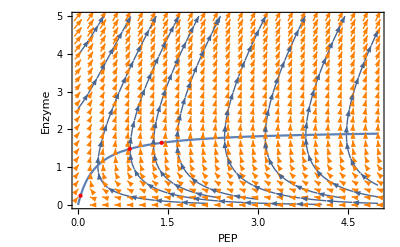

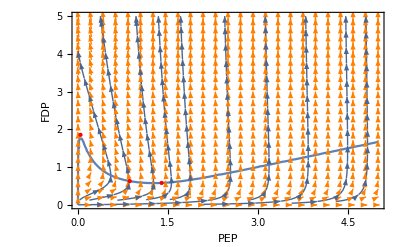

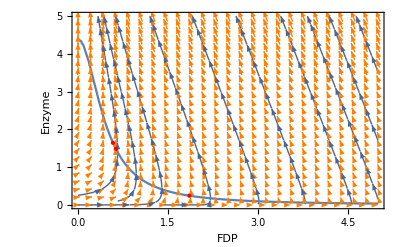

```mathematica
(*solve numerical system*)
eqsols = NSolve[f1[x,y,z]==0&&f2[x,y,z]==0&&f3[x,y,z]==0,{x,y,z},Reals];
(*get only poistive solutions*)
eqsols = {x,y,z}/.Select[eqsols,!MemberQ[Values[#],x_/;x<0]&]
f12d[x_,z_]:=flux1[z]-flux4[x]-flux5[x];
f22d[x_,y_]:=flux4[x]-flux3[x,y];
f32d[y_,z_]:=flux2[y]-d*z;

upl = 5;
vp1 = VectorPlot[{f12d[x,z],z},{x,0,upl},{z,0,upl},VectorPoints->Fine,VectorStyle->Orange,StreamPoints->10];
lp1 = ListPlot[Table[eqsols[[i,{1,3}]],{i,1,3}],PlotStyle->Directive[Red,PointSize[Large]]];
cp1=ContourPlot[f12d[x,z]==0,{x,0,upl},{z,0,upl}];
Show[{vp1,cp1,lp1},Axes-> True,AxesLabel-> {PEP,Enzyme},AspectRatio->1/GoldenRatio,PlotRange->{{0,upl},{0,upl}}]

vp2 = VectorPlot[{f22d[x,y],y},{x,0,upl},{y,0,upl},VectorPoints->Fine,VectorStyle->Orange,StreamPoints->10];
lp2 = ListPlot[Table[eqsols[[i,{1,2}]],{i,1,3}],PlotStyle->Directive[Red,PointSize[Large]]];
cp2=ContourPlot[f22d[x,y]==0,{x,0,upl},{y,0,upl}];
Show[{vp2,cp2,lp2},Axes-> True,AxesLabel-> {PEP,FDP},AspectRatio->1/GoldenRatio,PlotRange->{{0,upl},{0,upl}}]

vp3 = VectorPlot[{f32d[y,z],z},{y,0,upl},{z,0,upl},VectorPoints->Fine,VectorStyle->Orange,StreamPoints->10];
lp3 = ListPlot[Table[eqsols[[i,{2,3}]],{i,1,3}],PlotStyle->Directive[Red,PointSize[Large]]];
cp3=ContourPlot[f32d[y,z]==0,{y,0,upl},{z,0,upl}];
Show[{vp3,cp3,lp3},Axes-> True,AxesLabel-> {FDP,Enzyme},AspectRatio->1/GoldenRatio,PlotRange->{{0,upl},{0,upl}}]
```

```mathematica
(*tt = Table[Positive[Values[sol[[i]]]],{i,1,6}]
Select[Positive[Values[sol]],!MemberQ[#,False]&]*)

(*MemberQ[Table[Positive[{x,y,z}/.sol[[i]]],{i,1,1}],TrueQ,2]*)
```

{{0.244262,0.0417335,1.85613},{1.48446,0.863055,0.630648},{1.64602,1.39234,0.582071}}